# Fit vertex angles in stationary patterns from example simulation, measure domain sizes, and the number of vertices (corners) of each domain

## Setup

### Load format specifiers to import Comsol data

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->Automatic
];
```

## Import data

```mathematica
times=Join[{0},10^Range[0,5.6,0.1]];
```

```mathematica
dataE=Import[NotebookDirectory[]<>"/MinSwitchPMB-vonNeumannStats-usageExample.txt","Comsol2DSweep"];
data=dataE["mde+me"][[{1}]];
```

MinD density for example plot

```mathematica
dataD=Import[NotebookDirectory[]<>"/MinSwitchPMB-vonNeumannStats-usageExample.txt","Comsol2DSweep"];
dataMinD=dataD["md+mde"][[{1}]];
```

Color scheme RGB

```mathematica
colorMap={minD/1.5,minE,minE+minD/1.5/1.5};
```

## Image preparation

Skeleton of the network

```mathematica
branchIm=Table[Thinning@Binarize[Image[sim]//ImageAdjust],{sim,data}];
```

```mathematica
branchIm[[1]]
```

-Graphics-

## Analysis of triple vertices

## Find vertices

### Average branch widths

Determine average branch width by binarizing the experimental network image (cleanI) at half-maximum intensity, count the white pixels (width*length of network) and divide by the white pixels in the network skeleton (length of network because everywhere only one pixel wide)

```mathematica
width=N@Total@Flatten@Table[ImageData[Binarize[Image[sim]//ImageAdjust,0.5]],{sim,data}]/(Total@Flatten@(ImageData/@branchIm))
```

3.67045

Branch cross sections

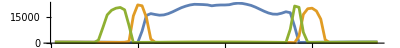

```mathematica
ListLinePlot[Transpose[data[[1]][[;;,;;;;30]]],AspectRatio->1/10,PlotRange->All]
```

### Determine branch points

The branch width is about 4 pixels, see below.
We prun branches shorter than 10 pixels because for their vertices no reliable angles can be determined.

```mathematica
branchImPrun=Pruning[#,10]&/@branchIm;
```

```mathematica
branchImPrun[[1]]
```

-Graphics-

```mathematica
branchPoints=MorphologicalBranchPoints/@branchImPrun;
```

```mathematica
branchPointCoords=ImageValuePositions[#,1]&/@branchPoints;
```

```mathematica
HighlightImage[branchImPrun[[1]],{AbsolutePointSize[3],branchPointCoords[[1]]}]
```

-Graphics-

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVertices=Table[Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@bpCoords,0.]]}]/@bpCoords,#[[-1]]>10&],{bpCoords,branchPointCoords}];
Length/@tripleVertices
```

{4}

### 4-fold vertices

```mathematica
quadrupleVerticesRaw=Table[Complement[branchPointCoords[[ind]],tripleVertices[[ind,All,1]]],{ind,Length@data}];
quadrupleVertices=Table[DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadVertices[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadVertices],I],{quadVertices,quadrupleVerticesRaw}];
Length/@quadrupleVertices
```

{0}

```mathematica
vertices=tripleVertices;
```

```mathematica
HighlightImage[branchIm[[1]],{AbsolutePointSize[5],tripleVertices[[1]]}]
```

-Graphics-

## Analysis of triple vertices

Experimental network data labeled by pixel positions

```mathematica
{dy,dx}=Dimensions@data[[1]];
```

```mathematica
dataPos=Table[{j-0.5,dy-i+0.5,#[[i,j]]},{i,1,Dimensions[#][[1]]},{j,1,Dimensions[#][[2]]}]&/@data;
```

### Measurement functions

Fit the vertex by assuming Gaussian cross-sections of the vertex arms:

```mathematica
ClearAll@lossF;
lossF[vertexData_,x1_?NumericQ,x2_?NumericQ,angles_?VectorQ]:=
Total[
Function[d,
(d[[3]]-Exp[-#/((width/2)^2/Log[2])])^2&@Min[If[Length@#==0,{1000},#]&@((Norm[d[[{1,2}]]-{x1,x2}]^2-((d[[{1,2}]]-{x1,x2}).{Cos[#],Sin[#]})^2)&/@
Select[angles,
Function[angle,((d[[{1,2}]]-{x1,x2}).{Cos[angle],Sin[angle]})>-10^-10]
])
]]/@vertexData[[2]]];
```

```mathematica
ClearAll@measureData;
measureData[vertexData_,armNumber_]:=
Block[
{
dataW,
iniCond,
iniCondClean,
vars,
sol,sol2,
fitSuccess=1,
fit
},
(*get initial conditions for the angles of the vertex arms by making a radial histogram and finding its peaks*)
dataW=WeightedData[#[[All,1]],#[[All,2]]]&@({PlanarAngle[{0,0}->{{1,0},#[[{1,2}]]}],#[[3]]}&/@Transpose[{vertexData[[2,All,1]],vertexData[[2,All,2]],Rescale@vertexData[[2,All,3]]}]);
iniCond=If[#[[1]]>Pi,{#[[1]]-2Pi,#[[2]]},#]&/@({0.05+(HistogramList[dataW,{0,2Pi,0.2}][[1,#[[1]]]]),#[[2]]}&/@(FindPeaks[Last@HistogramList[dataW,{0,2Pi,0.2}],1,0,0,Padding->"Periodic"]));
(*take mean of peaks that lie close together; map angles onto [-Pi,Pi] range*)
iniCondClean=If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&/@
SortBy[DeleteDuplicates@Table[
Mean[
Select[Join[iniCond,{#[[1]]-2Pi,#[[2]]}&/@iniCond,{#[[1]]+2Pi,#[[2]]}&/@iniCond],Min[Abs[#[[1]]-ini[[1]]]<0.5&]]
],{ini,iniCond}],#[[2]]&][[All,1]];
If[Length[iniCondClean]<3,
sol=I,
iniCond=iniCondClean[[-armNumber;;]];
vars=Symbol["a"<>ToString[#]]&/@Range[Length@iniCond];
Quiet@Check[sol=Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2];,fitSuccess=0;];
(*Try a second time if it failed*)
If[fitSuccess==0,
sol2=Check[Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2,Method->"PrincipalAxis"],I];
sol=sol2;
];
];
If[sol===I,
I,
fit=Join[{vertexData[[1,1]]+x1,vertexData[[1,2]]+x2}/.sol,Sort[If[#<-Pi,#+2Pi,If[#>Pi,#-2Pi,#]]&/@(vars/.sol)]];
If[Min[Abs@Differences[fit[[2;;]]]]<0.01,
I,
fit]
]
];
```

### Analysis

The fit data for each vertex is taken as the data points within a 15 pixel large radius around the branch point. If a second branch point lies closer than 15 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[dataPos[[#,Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[15,vertex[[2]]]&]},{vertex,tripleVertices[[#]]}]&/@Range[Length@data];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[1,Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data[[1]]}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw=Table[ParallelTable[measureData[data,3],{data,vertData},Method->"FinestGrained"],{vertData,vertex3Data}];
```

```mathematica
fittedVertices=Table[Select[Transpose[{Range@Length@#,#}&@vertMeas],ListQ[#[[2]]]&][[All,1]],{vertMeas,vertex3MeasurementsRaw}];(*indices of successfully fitted vertices*)
failedVertices=Table[Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],#[[2]]==I&][[All,1]],{vertMeas,vertex3MeasurementsRaw}];(*indices of vertices that couldn't be fitted*)
vertex3Measurements=Table[DeleteCases[vertMeas,I],{vertMeas,vertex3MeasurementsRaw}];(*fitted vertices*)
Length/@vertex3Data
Length/@vertex3Measurements
```

{4}

{4}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[1,fittedVertices[[1]]]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[1,Floor@i,;;2]]-(tripleVertices[[1,fittedVertices[[1]]]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[1,fittedVertices[[1]]]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[1,fittedVertices[[1]]]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[1,Floor@i]],1]]]
],{i,1,Length@vertex3Measurements[[1]]}]
```

```mathematica
Show[
HighlightImage[Image[data[[1]]]//ImageAdjust,{AbsolutePointSize[5],tripleVertices[[1]]}],
Graphics[Join[{Darker@Red,Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements[[1]],1],
{RGBColor[{255,150,20}/255]}]]
]
```

-Graphics-

```mathematica
angles3=Table[(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertMeas[[All,3;;]]),{vertMeas,vertex3Measurements}];
```

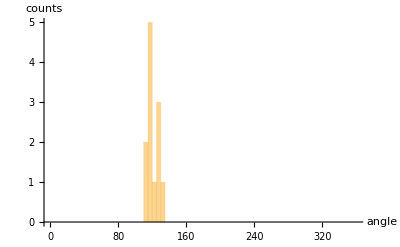

```mathematica
Histogram[{
Flatten[angles3,2]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles3,2]]
```

120.

```mathematica
StandardDeviation[Flatten[angles3,2]]
```

7.21556

#### FitList – Expected result

```mathematica
vertex3MeasurementsRaw={{{56.49866740165297,62.497402742201906,-2.5499074221870943,-0.5326291837056021,1.54736602864004},{37.505937573352,50.51456321716136,-1.398249444180277,0.5259635100764757,2.579308947203442},{41.5033972465016,23.500759132336317,-2.5287469258010673,-0.2873653678272658,1.7259903689034892},{67.51015090272561,18.502935503889947,-0.9909638426554405,0.9389728726004795,3.039537939291242}}};
```

### Fit result, examplified for first simulation

```mathematica
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1]],dataMinD[[1]]}))
```

-Graphics-

```mathematica
Show[
Image[Map[{0,1,1}*#&,data[[1]],{2}]/Max[Flatten@data[[1]]]],
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+8{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements[[1]],1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices[[1]]]]
]
```

-Graphics-

## Bubble statistics

Determine the bubbles alone:

```mathematica
bubblesIm=Pruning[Pruning@#,Infinity]&/@branchIm;
bubblesIm[[1]]
```

-Graphics-

```mathematica
bubbles=MorphologicalComponents[ColorNegate@#,"CornerNeighbors"->False]&/@bubblesIm;
```

```mathematica
bubbles[[1]]//Colorize
```

-Graphics-

## Analyze domain-size and hole correlation

```mathematica
boundaryDomains=DeleteDuplicates[Flatten[{#[[1]],#[[-1]],#[[All,1]],#[[All,-1]]}]]&/@bubbles;
```

```mathematica
bubbleInds=Complement[DeleteDuplicates[Flatten[bubbles[[#]]]],boundaryDomains[[#]]]&/@Range[Length@data];
```

```mathematica
bubbleMeas=Flatten[ComponentMeasurements[bubbles[[#]],{"Area","Holes"}][[bubbleInds[[#]]]]&/@Range[Length@data],1];
```

```mathematica
bubbleMeas
```

{1→{1439.88,0}}

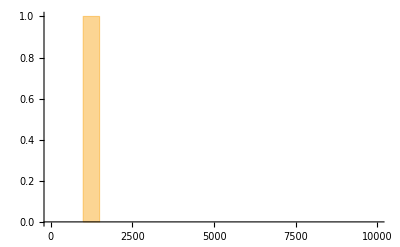

```mathematica
Histogram[{Select[Values@bubbleMeas,#[[2]]==0&][[All,1]],Select[Values@bubbleMeas,#[[2]]==1&][[All,1]]},{0,10000,500}]
```

## Number of corners of each domain

Use only internal bubbles not in contact with the boundary because those bubbles are not expected to have 6 corners.

In this small simulation, no internal bubble exists.

```mathematica
boundaryDomains=DeleteDuplicates[Flatten[{#[[;;10]],#[[-10;;]],#[[All,;;10]],#[[All,-10;;]]}]]&/@bubbles;
```

```mathematica
internalBubbleInds=Complement[DeleteDuplicates[Flatten[bubbles[[#]]]],boundaryDomains[[#]]]&/@Range[Length@data];
```

```mathematica
cornerNumber=Flatten[Table[
Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,bubbles[[sim]],{2}]],DiskMatrix[1]]},
If[b==10,
-1(*that is the outside of the bubbles*),
Total@Flatten[ImageData[branchPoints[[sim]]]*ImageData[mask]]
]
],
{b,internalBubbleInds[[sim]]}],#>0&],
{sim,Length@data}],1];
```

```mathematica
Histogram[cornerNumber,{0.5,10,1}]
```

-Graphics-

```mathematica
Mean[cornerNumber]
```

Mean[{}]

```mathematica
StandardDeviation[cornerNumber]
```

StandardDeviation::shlen: The argument {} should have at least two elements.

StandardDeviation[{}]